```mathematica
Clear[MulSum]
MulSum[a_?NumericQ,b_?NumericQ,n_?NumericQ]:=FracExp[FracExp[a,-n]+FracExp[b,-n],n];
```

```mathematica
a=2+0.1I;b=7+0.1I;
MulSum[a,b,0]
MulSum[a,b,1]
```

9.+0.2 ⅈ

13.99+0.9 ⅈ

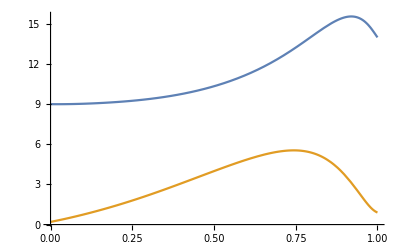

```mathematica
lbp=-0.5;
Plot[{Re[MulSum[a,b,n]],Im[MulSum[a,b,n]]},{n,0,1},PlotRange->Full]
```

```mathematica
Needs["NumericalCalculus`"];
NormalMulSum[a_,b_,n_?NumericQ]=(Re[MulSum[a,b,n]]-Re[MulSum[a,b,0]])/(Re[MulSum[a,b,1]]-Re[MulSum[a,b,0]]);
DNormalMulSum[a_,b_,n_?NumericQ]:=ND[NormalMulSum[a,b,ns],ns,n];

ObstacleSize[a_,b_]:=
NIntegrate[Max[0,-DNormalMulSum[a,b,n]],{n,0,1},PrecisionGoal->2];

ObstaclePlot[a_,b_]:=Module[{sp=NormalMulSum[a,b,0],ep=NormalMulSum[a,b,1]},
Show[
Plot[NormalMulSum[a,b,n], {n,0,1},PlotRange->Full],
Plot[If[DNormalMulSum[a,b,n]<0, NormalMulSum[a,b,n],0], {n,0,1},Filling->Axis,PlotStyle->None],
Graphics[Text[ObstacleSize[a,b],{0.1,1.2}]]
]
]
```

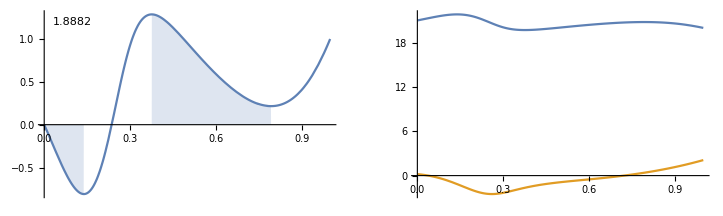

```mathematica
a=20+0.1I;b=1+0.1I;
GraphicsRow[{
ObstaclePlot[a,b],
Plot[{Re[MulSum[a,b,n]],Im[MulSum[a,b,n]]},{n,0,1},PlotRange->Full]
}]
```

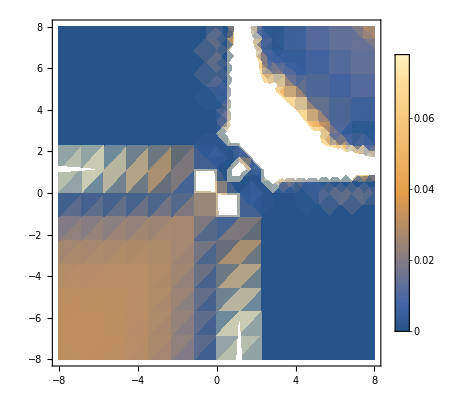

```mathematica
DensityPlot[ObstacleSize[a,b],{a,-8,8},{b,-8,8},
PlotLegends->Automatic]
```